```mathematica
Quit[]
```

```mathematica
Needs@"RunningCouplings`"
```

```mathematica
?"RunningCouplings`*"
```

```mathematica
RunningCouplings["SM", "TopQuarkPoleMassScale"]
```

<|RenormalizationScheme→MSbar,RenormalizationScale→172.4,g→0.6476520.0000240.000024,gp→0.3585420.0000190.000021,g3→1.1630.0050.004,yt→0.9310.0040.004,yc→0.003390.000100.00010,yu→6.70.81.510^-6,yb→0.015500.000130.00016,ys→0.0002920.0000160.000035,yd→0.00001465056151,ytau→0.009994477,ymu→0.00058837806426,ye→2.7929700.0000260.00002010^-6,lambda→0.126070.000290.00029,m2→-8612.23.23.,v→246.60450.00340.0034,Lambda→1.23400.00280.002810^8|>

```mathematica
RunningCouplings[
"MSSM",
10^7,
"TanBeta"->10,
"LightestNeutrinoMass"->10^-12,
"NeutrinoMassHierarchy"->"Normal",
"NeutrinoMassOperator"->"Dirac",
"SupersymmetryScale"->10^4
]
```

<|RenormalizationScheme→DRbar,RenormalizationScale→10000000,SupersymmetryScale→10000,TanBeta→10,g1→0.50850.00150.0015,g2→0.6410.0050.005,g3→0.8580.0130.014,yu→4.80.61.110^-6,yc→0.002180.000070.00007,yt→0.6900.0130.013,yd→0.00009240,ys→0.001840.000110.00022,yb→0.09740.00130.0014,ye→0.000026772827,ymu→0.005640.000060.00006,ytau→0.09590.00100.0009,y1→6.0170.0090.02110^-15,y2→5.220.210.2310^-14,y3→3.020.050.0510^-13,CKM→<|Parametrization→Wolfenstein,Lambda→0.226540.000340.0011,A→0.7320.0290.018,RhoBar→0.1690.0190.04,EtaBar→0.3610.0260.027|>,PMNS→<|Parametrization→Standard,Theta12→0.580.040.04,Theta23→0.850.160.05,Theta13→0.1500.0070.007,Delta→3.403.10.|>|>

```mathematica
RunningGaugeCoupling[
{"MSSM", 3},
10^12,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]
```

0.7490.0090.009

```mathematica
Table[
RunningGaugeCoupling[
{"MSSM", 3},
10^x,
"TanBeta"->10,
"SupersymmetryScale"->10^4
],
{x,{10,12,14}}
]
```

{0.7870.0100.011,0.7490.0090.009,0.7150.0080.008}

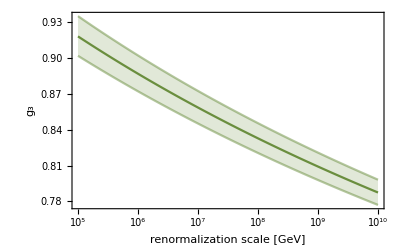

```mathematica
LogLinearPlot[
{
RunningGaugeCoupling[{"MSSM",3},scale]["Value"],
RunningGaugeCoupling[{"MSSM",3},scale]["Interval"]//Min,
RunningGaugeCoupling[{"MSSM",3},scale]["Interval"]//Max
},
{scale,10^5,10^10},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","g_3"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.4]],
Directive[ColorData["DarkRainbow"][0.4],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.4],Opacity@0.5]
}
]
```

```mathematica
RunningYukawaCoupling[
{"MSSM","U",3},
10^12.5,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]
```

0.5830.0130.014

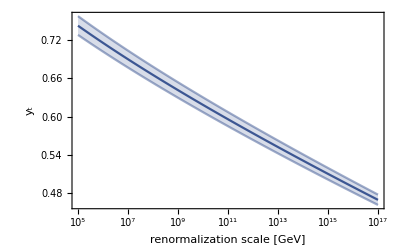

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","U",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_t"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0]],
Directive[ColorData["DarkRainbow"][0],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0],Opacity@0.5]
}
]
```

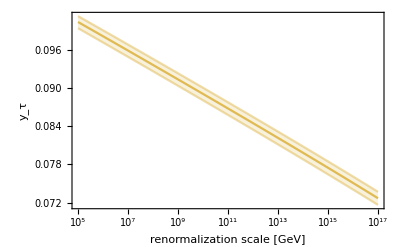

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","E",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_τ"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.7]],
Directive[ColorData["DarkRainbow"][0.7],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.7],Opacity@0.5]
}
]
```

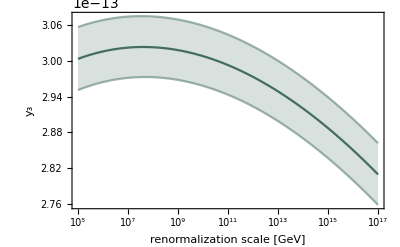

```mathematica
LogLinearPlot[
{
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Value"],
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningYukawaCoupling[
{"MSSM","V",3},
scale,
"TanBeta"->10,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","y_3"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.2]],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5]
}
]
```

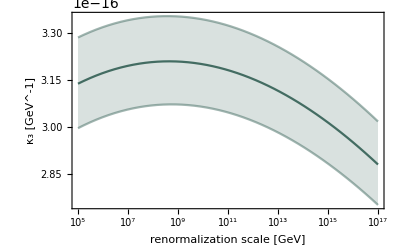

```mathematica
LogLinearPlot[
{
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Value"],
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningWeinbergOperator[
{"MSSM",2},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","κ_3 [GeV^-1]"},
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.2]],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.2],Opacity@0.5]
}
]
```

```mathematica
RunningMixingParameter[
{"MSSM","CKM","A"},
10^16,
"SupersymmetryScale"->10^4
]
```

0.6360.0250.016

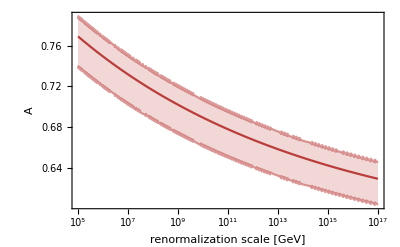

```mathematica
LogLinearPlot[
{
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Value"],
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Interval"]//Min,
RunningMixingParameter[
{"MSSM","CKM","A"},
scale,
"SupersymmetryScale"->10^4
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","A"},
PlotRange->All,
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.9]],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5]
}
]
```

```mathematica
RunningMixingParameter[
{"MSSM","PMNS","Theta12"},
10^16,
"TanBeta"->50,
"SupersymmetryScale"->10^4
]
```

0.570.040.04

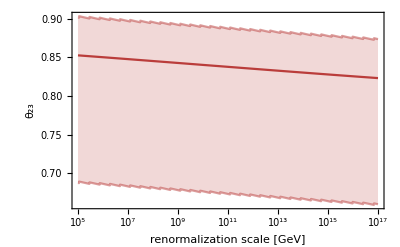

```mathematica
LogLinearPlot[
{
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Value"],
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Interval"]//Min,
RunningMixingParameter[
{"MSSM","PMNS","Theta23"},
scale,
"TanBeta"->50,
"SupersymmetryScale"->10^4,
"LightestNeutrinoMass"->10^-12
]["Interval"]//Max
},
{scale,10^5,10^17},
Filling->{2->{3}},
Frame->True,
FrameLabel->{"renormalization scale [GeV]","θ_23"},
PlotRange->All,
PlotStyle->{
Directive[ColorData["DarkRainbow"][0.9]],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5],
Directive[ColorData["DarkRainbow"][0.9],Opacity@0.5]
}
]
```